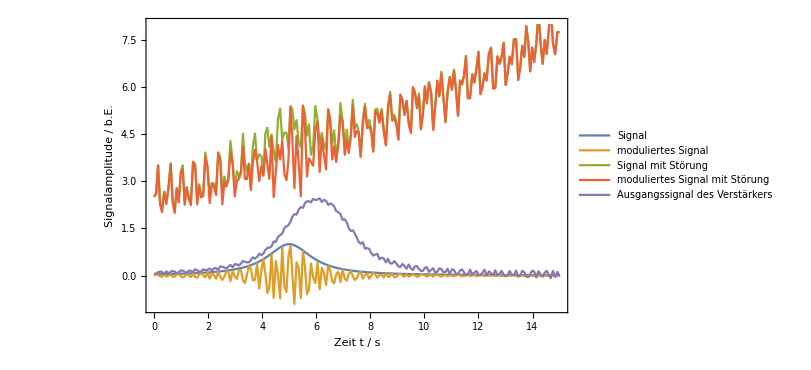

```mathematica
f=30;
refsig[t_]=Sin[f*2π t];
sig[t_]=1/(1+(t-5)^2);
stö[t_]=2.5+0.2t+0.01 t^2+0.5Sin[2.2*2π t]+0.5Sin[8.6*2π t];
sigmst[t_]=sig[t]+stö[t];
modsig[t_]=refsig[t]*sig[t];
modsigmst[t_]=modsig[t]+stö[t];
produkt[t_]=modsigmst[t]*refsig[t];

p=Plot[
{sig[t],modsig[t],sigmst[t],modsigmst[t],3*NIntegrate[produkt[y],{y,t-10*(2π)/f,t}]},
{t,0,15},
PlotRange->{-1,8},
PlotPoints->600,
ImageSize->600,
MaxRecursion->3,
PlotLegends->{"Signal","moduliertes  Signal","Signal mit Störung","moduliertes \n Signal mit Störung","Ausgangssignal \n des Verstärkers"},
Frame->True,
FrameLabel->{"Zeit t / s","Signalamplitude / b.E."},
BaseStyle->17
]
```

```mathematica
Export[NotebookDirectory[]<>"../img/lockin.pdf",p]
```

/home/moritz/FP1/1002-Halbleiter/stuff/../img/lockin.pdf